## Normal Modes of Coupled Oscillators

Student IDs = { #_1,#_2 } | Total Mark = mark | Marker =

## Syntax Reminders

Evaluate expressions by selecting the cell bracket or positioning the mouse anywhere within an expression, and hit ⇧-⏎ on the keyboard or ⌤  on the numpad.

The symbol % denotes the previous output.

For numerical expressions:  exact input ⟹ exact output,  approx input ⟹ approx output

Entering Two-Dimensional Expressions can be done with the Basic Math Assistant palette or with keyboard shortcuts

2D expression | 1D input | Keyboard entry
x^m | x^m | xCtrl[^] m
x/y | x/y | x Ctrl[/] y
x_i | x_i | x Ctrl[_] i

### Getting Help

The Documentation Center, under the Help menu, gives you access to Mathematica’s on-line documentation. An overview of Mathematica is presented in the First Five Minutes with Mathematica section.

Long function names can be difficult to enter and remember,  Complete Selection Ctrl[k] and Make Template Ctrl[K] under the Edit Menu increases the speed, correctness, and convenience of Notebooks.

Alternatively one can use a Palette such as the Basic Math Assistant.

### Replacement Rules

Solutions to equations are returned as a list of lists of replacement rules:

```mathematica
sol=Solve[{a x^2+b y==0,c x+d y==0},{x,y}]
```

{{y→0,x→0},{y→-(b c^2)/(a d^2),x→(b c)/(a d)}}

To use the solutions, the ReplaceAll (/.) command is used. Here we substitute both solutions into both equations:

```mathematica
{a x^2+b y==0,c x+d y==0}/.sol
```

(True | True
True | True)

Substitute the second (or Last) solution into the variable x:

```mathematica
x/.sol⟦2⟧
```

(b c)/(a d)

Remove this definition:

```mathematica
Remove[sol]
```

### Protected Symbols

Certain symbols, such as D (which denotes the partial derivative) are protected:

```mathematica
D=2
```

Set::wrsym: Symbol D is Protected.

2

If one uses lower-case letters this problem is avoided.

An alternative is to use, say, script letters, available in the SpecialCharacters palette:

```mathematica
𝒟=2
```

2

Note that most special characters have Esc aliases (or keyboard shortcuts):  eg  𝒟 ← EscscDEsc,  while  𝔻 ← EscdsDEsc  etc…

### Basic List Operations

One can extract parts of an expression expr using Part or using the shorthand form expr[[n]] or expr⟦n⟧, with ⟦ ← Esc[[Esc :

```mathematica
{x,y,z}⟦2⟧
```

2

One can extract multiple entries using a list of indices:

```mathematica
{x,y,z}⟦{2,3,2,1}⟧
```

{y,z,y,x}

A matrix is a list of lists (rows).

Here is the first row of the matrix (a | b
c | d)={{a,b},{c,d}} :

```mathematica
({{a, b}, {c, d}})⟦1⟧
```

{a,b}

Here is the (2,1) element:

```mathematica
({{a, b}, {c, d}})⟦2,1⟧
```

Swap the first and second rows:

```mathematica
({{a, b}, {c, d}})⟦{2,1}⟧
```

The easiest way of swapping columns is to take the Transpose of the matrix first.

### Generating Matrices

One can construct matrices in a variety of ways. For now, we will do it either:

by hand, typing in a list of lists;

using the Basic Math Assistant palette;

using Insert ▸ Table/Matrix ▸ New…  ;

or using the Table command.

Construct a 2×3 matrix as a list of lists:

```mathematica
{{a,b,c},{d,e,f}}
```

(a | b | c
d | e | f)

Use Table to construct a general 4×6 matrix:

```mathematica
Table[Subscript[a, i,j],{i,4},{j,6}]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5) | a_(1,6)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5) | a_(2,6)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5) | a_(3,6)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5) | a_(4,6))

If you are not using TraditionalForm for output, you can use MatrixForm to display matrices:

```mathematica
MatrixForm@%
```

### Defining Functions

Define the function, f(x)=x^2+1:

```mathematica
f[x_]:=x^2+1
```

Note that the symbol f went from blue = undefined to black = defined.

Here is f(2):

```mathematica
f[2]
```

5

Here is f({x,y}):

```mathematica
f[{x,y}]
```

{x^2+1,y^2+1}

To see what definitions are associated with a symbol, use ?

```mathematica
?f
```

Global`f

f[x_]:=x^2+1

Clear this definition:

```mathematica
Clear[f]
```

The symbol f has now returned to being blue:

```mathematica
?f
```

Global`f

### Defining Vector Functions

Define g(x,y)=(x y,x^2-y^2), a vector function (or map) g:ℝ^2→ℝ^2:

```mathematica
g[{x_,y_}]:={x y,x^2-y^2}
```

Compute g(a,b):

```mathematica
g[{a,b}]
```

{a b,a^2-b^2}

Note that g takes a vector and returns a vector. This is useful when composing such functions.

Compute g∘g(x,y):

```mathematica
g@g[{x,y}]//Simplify
```

{x y (x^2-y^2),-x^4+3 x^2 y^2-y^4}

Remove this definition:

```mathematica
Clear[g]
```

## Normal Modes of Coupled Oscillators

In this section you will explore the natural frequencies and normal modes of a system of n coupled oscillators. The case with n=3 looks like:

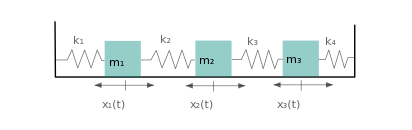

The parameters k_i are the spring constants; m_i are the masses of the blocks; and x_i(t) are the displacements from the equilibrium positions.

### Making equations Listable

For this assignment, we modify Equal so that Listable operations are automatically applied to both sides of any equality:

```mathematica
Unprotect[Equal];
```

```mathematica
listableQ[f_]:=MemberQ[Attributes[f],Listable]
```

```mathematica
Equal/:lhs:f_Symbol?listableQ[___,_Equal,___]:=Thread[Unevaluated[lhs],Equal]
```

```mathematica
Protect[Equal];
```

These definitions are initialization cells. Now we can directly manipulate equations.

Manually solve for x in y==m x+c:

```mathematica
y==m x+c
```

y==c+m x

```mathematica
%-c
```

y-c==m x

```mathematica
%/m
```

(y-c)/m==x

### Equations of Motion: Fixed end-points

For a system of n coupled oscillators, by considering the free-body diagram for mass m_i, the equation of motion is

m_i x''_i(t) ==k_(i+1)(x_(i+1)(t)-x_i(t))-k_i (x_i(t)-x_(i-1)(t))

When the end-points are fixed the boundary conditions read

x_0(t)==x_(n+1)(t)==0

Collecting terms multiplying x_i(t) the equation of motion for m_i reads

m_i x''_i(t) ==k_i x_(i-1)(t)-(k_i+k_(i+1))x_i(t)+k_(i+1)x_(i+1)(t),1≤i≤n.

Applying the boundary conditions, we express the equations in matrix form:

(m_1 x''_1(t)
m_2 x''_2(t)
⋮
m_(n-1)x''_(n-1)(t)
m_n x''_n(t))== (-k_1-k_2 | k_2 | 0 | ⋯ | 0
k_2 | -k_2-k_3 | k_3 | ⋱ | ⋮
0 | k_3 | -k_3-k_4 | ⋱ | 0
⋮ | ⋱ | ⋱ | ⋱ | k_n
0 | ⋯ | 0 | k_n | -k_n-k_(n+1)).(x_1(t)
x_2(t)
⋮
x_(n-1)(t)
x_n(t))

### Equal masses and equal spring constants

Symbolic analysis for general values for k_i and m_i is complicated. We will firstly examine the case where all the k_i are equal to k and all the m_i equal m.

Obtain the equation of motion for the i^th mass when all the k_i→k and m_i→m using a substitution rule:

```mathematica
Subscript[m, i] Subscript[x, i]''(t) ==Subscript[k, i+1] (Subscript[x, i+1](t)-Subscript[x, i](t))-Subscript[k, i] (Subscript[x, i](t)-Subscript[x, i-1](t))/.{Subscript[m, i_]->m,Subscript[k, i_]->k}//Simplify
```

m x_i''(t)==k (x_(i-1)(t)-2 x_i(t)+x_(i+1)(t))

Divide through by k:

```mathematica
%/k
```

(m x_i''(t))/k==x_(i-1)(t)-2 x_i(t)+x_(i+1)(t)

Introducing the frequency (time-scale), ω=√(k/m), (i.e., rescaling time by this factor), the equations can be cast into the dimensionless form:

x''_i(t) ==x_(i-1)(t)-2x_i(t)+x_(i+1)(t),1≤i≤n.

Taking into account the boundary conditions, the equation of motion for each of the n masses reads

```mathematica
Subscript[ℰ, n_,1]:=Subscript[x, 1]''(t)==Subscript[x, 2](t)-2 Subscript[x, 1](t)
```

```mathematica
Subscript[ℰ, n_,i_]:=Subscript[x, i]''(t)==Subscript[x, i-1](t)-2 Subscript[x, i](t)+Subscript[x, i+1](t)/;1<i<n
```

```mathematica
Subscript[ℰ, n_,n_]:=Subscript[x, n]''(t)==Subscript[x, n-1](t)-2 Subscript[x, n](t)
```

Equations

Compute the set of equations for n=4. [1 Mark]

Solution

Matrix form of the equations

Since the motion of each mass is expected to be simple-harmonic, one looks for a solution of the form (this is called an ansätz):

```mathematica
Subscript[x, i_](t_)=Subscript[c, i] cos(Ω t);
```

Enter the ansätz and then simplify the set of equations for n=4. (Hint: you should find that cos(Ω t) appears on both sides of each equation. Dividing through by cos(Ω t) should help.) [2 Marks]

Turn the resulting set of equations into a matrix equation (CoefficientArrays can help here) by filling in the blanks: [2 Marks]

```mathematica
({{2, -1, 0, 0}, {□, □, □, □}, {□, □, □, □}, {□, □, □, □}}).({{Subscript[c, 1]}, {Subscript[c, 2]}, {□}, {□}})==□ ({{Subscript[c, 1]}, {□}, {□}, {□}})
```

The matrix on the left-hand side is called the normal-mode matrix. Recall that the eigenvalues, λ, and eigenvectors, x, of a matrix 𝒜 satisfy 𝒜.x=λ x.

What is the relationship between the eigenvalues and the natural frequencies, Ω, of the oscillating system? [1 Mark]

What is the relationship between the energy of the normal-mode and its frequency? (Hint: the kinetic energy of each mass is T∝(v_i(t))^2 and the motion, x_i(t), is assumed simple-harmonic.) [1 Mark]

Assign ℳ_4 to be the 4×4 normal-mode matrix. Compute the eigenvalues of ℳ_4. Note that the exact values are generated. [2 Marks]

Solution

General normal-mode matrix

By looking at ℳ_4 you should be able to deduce the structure of the general normal-mode matrix, ℳ_n for a system of n masses. This is a sparse matrix consisting of non-zero bands. One can use SparseArray and Band to define such matrices.

Use SparseArray to define the general normal-mode matrix, ℳ_n of size n×n. Check that your procedure correctly generates the 7×7 normal-mode matrix. [2 Marks]

Obtain the numerical values of the eigensystem of ℳ_5 by applying Eigensystem to N[ℳ_5], which returns the list of eigenvalues and the list of (row) eigenvectors. (Note: you can get rid of the small complex values that may arise in the numerical solution by using Chop). [1 Mark]

In physical systems the ordering of the energies is relevant. Sort the eigensystem in order of increasing eigenvalue (Hint: Sort and Transpose can assist here). [1 Mark]

Solution

Visualizing the normal-mode amplitudes

The following code for ModePlot uses ListPlot to display the i-th eigenvector for a system of n masses. The endpoints x_0=0 and x_(n+1)=0 have been joined to the i-th eigenvector using the Join command. The (normal-mode) oscillation frequencies are computed from the (square root) of the corresponding eigenvalues:

```mathematica
ModePlot[n_,i_]:=Module[{Λ,P},{Λ,P}=Transpose[Sort[Transpose[Eigensystem[N[Subscript[ℳ, n]]]]]];ListPlot[Join[{0},P⟦i⟧,{0}],Joined->True,PlotLabel->"Ω="<>ToString[√Λ⟦i⟧],Mesh->All,DataRange->{0,n+1},PlotRange->3/(2 √n) {-1,1}]]
```

Display the set of normal modes for n=5 using ModePlot. [1 Mark]

What is the relationship between the number of (interior) nodes, the eigenvalue number, and the frequency (and hence energy) or each mode? [1 Mark]

In light of the above graphics, what do the eigenvectors represent physically? In other words, relate the plots of the normal modes to the displacements of the masses from their equilibrium positions, x_i(t). [1 Mark]

Use ModePlot and TabView to visualize modes 1, 5, 10, and 50. What do these plots remind you of? (Analogies are very important in physics!) [2 Marks]

Display a plot of frequency versus mode number for n=50 using ListPlot. [1 Mark]

Solution

Visualizing the dynamics of normal-modes

DynamicModePlot uses ListPlot to display the eigenmodes as a function of t:

```mathematica
DynamicModePlot[n_,i_][t_]:=Module[{Λ,P},{Λ,P}=Transpose[Sort[Transpose[Eigensystem[N[Subscript[ℳ, n]]]]]];ListPlot[Tooltip[Join[{0},P⟦i⟧ Cos[Λ⟦i⟧ t],{0}],i],Joined->True,PlotLabel->"Ω="<>ToString[√Λ⟦i⟧],Mesh->All,DataRange->{0,n+1},PlotRange->3/(2 √n) {-1,1}]]
```

Use Manipulate to visualize the dynamics of the i-th eigenmode as a function of t for n=5 using DynamicModePlot. [1 Mark]

Solution

General Formula

Consider computing the eigenvalue of ℳ_n for arbitrary n. The eigenvalues are determined by the characteristic equation, Det[ℳ_n-λ ℐ_n]==0,

|2-λ | -1 | 0 | ⋯ | 0
-1 | 2-λ | -1 | ⋱ | 0
0 | -1 | 2-λ | ⋱ | 0
⋮ | ⋱ | ⋱ | ⋱ | -1
0 | ⋯ | 0 | -1 | 2-λ|==0

This determinant satisfies a simple linear recurrence relation (as can be seen from its Laplace or cofactor expansion):

𝒟_n==(2-λ)𝒟_(n-1)-𝒟_(n-2)

with initial conditions 𝒟_0==1 and 𝒟_1=2-λ. The general solution can be shown to be

𝒟_n=(sin((n+1)θ))/(sin(θ))

where

λ==4 sin^2(θ/2)==(2 sin(θ/2))^2==2-2cos(θ)

Eigenvalues require that 𝒟_n==0, so

(n+1)θ==i π⟹θ==(i π)/(n+1)

Hence the general formula for the frequencies (i.e., the square root of the eigenvalues) is

Ω_i=2 sin((i π)/(2 (n+1)))

where Ω_i is the frequency of the i-th mode for a system of n masses.

Verify that 𝒟_n==(2-λ)𝒟_(n-1)-𝒟_(n-2) for n==6. Hint: 𝒟_n==Det[ℳ_n-λ ℐ_n] can be obtained using CharacteristicPolynomial. [1 Mark]

Verify that 𝒟_n==sin((n+1)θ)/sin(θ) for λ→4 sin^2(θ/2) for n=2,3,…,6. [1 Mark]

Verify that Ω_i=2 sin((i π)/(2 (n+1))) agrees with direct computation of the frequencies for n=10. [1 Mark]

Solution

One end free

Consider equations of motion for the case where one end is free. When one end-point is free, say mass m_n, there is no spring k_(n+1).

Suitably modify ℳ_n and ModePlot in this case. (Note: be careful with the boundary conditions which are included in the code for ModePlot). [2 Marks]

Examine the case of 10 masses by plotting a few of the normal modes. Compare the behaviour to that with both ends fixed. [2 Marks]

Solution